# Unit vectors in 2D bipolar coordinates

## Katharine Long Texas Tech University

### Define coordinates

x-y coordinates in terms of u∈[-∞,∞] and v∈[-π,π]

```mathematica
R[u_,v_]={Sinh[u],Sin[v]}/(Cosh[u]+Cos[v])
```

{(sinh(u))/(cosh(u)+cos(v)),(sin(v))/(cosh(u)+cos(v))}

### Find unit vectors

#### Unit vector (ê)_u

```mathematica
dRdu[u_,v_]=D[R[u,v],u]//FullSimplify
```

{(cosh(u) cos(v)+1)/(cosh(u)+cos(v))^2,-(sinh(u) sin(v))/(cosh(u)+cos(v))^2}

Scale factor

```mathematica
hu[u_,v_]=Sqrt[dRdu[u,v].dRdu[u,v]]//FullSimplify//PowerExpand
```

1/(cosh(u)+cos(v))

```mathematica
eu[u_,v_]=dRdu[u,v]/hu[u,v]
```

{(cosh(u) cos(v)+1)/(cosh(u)+cos(v)),-(sinh(u) sin(v))/(cosh(u)+cos(v))}

#### Unit vector (ê)_v

```mathematica
dRdv[u_,v_]=D[R[u,v],v]//FullSimplify
```

{(sinh(u) sin(v))/(cosh(u)+cos(v))^2,(cosh(u) cos(v)+1)/(cosh(u)+cos(v))^2}

```mathematica
hv[u_,v_]=Sqrt[dRdv[u,v].dRdv[u,v]]//FullSimplify//PowerExpand
```

1/(cosh(u)+cos(v))

```mathematica
ev[u_,v_]=dRdv[u,v]/hv[u,v]
```

{(sinh(u) sin(v))/(cosh(u)+cos(v)),(cosh(u) cos(v)+1)/(cosh(u)+cos(v))}

### Set up plots of coordinate lines

```mathematica
uLim = ArcSinh[4];
```

```mathematica
xyLim={{-4,4},{-4,4}};
```

```mathematica
linewidth=Thickness[0.0025];
```

```mathematica
uCurves = ParametricPlot[Table[R[u,v],{u,-uLim,uLim,uLim/10}],{v,-Pi,Pi},PlotRange->xyLim,PlotStyle->{linewidth,RGBColor[0.4,0.4,0.8]}];
```

```mathematica
vCurves = ParametricPlot[Table[R[u,v],{v,-Pi,Pi,Pi/10}],{u,-uLim,uLim},PlotStyle->{linewidth,RGBColor[0.8,0.4,0.4]},PlotRange->xyLim];
```

#### Show both coordinates

Curves of constant u are in blue. Curves of constant v are in red.

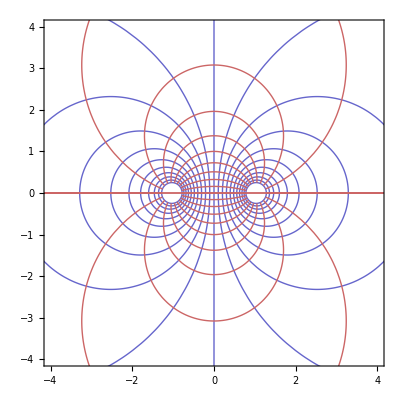

```mathematica
coords=Show[uCurves,vCurves]
```

### Write a function to draw unit vectors

```mathematica
showVecs[u_,v_]:=Graphics[{
Thick,
{Blue,Arrow[{R[u,v],R[u,v]+ev[u,v]}]},
{Red,Arrow[{R[u,v],R[u,v]+eu[u,v]}]}
},PlotRange->xyLim
]
```

## Interactive unit vectors

```mathematica
Manipulate[Show[coords,showVecs[u,v]],{u,-uLim,uLim},{v,-Pi,Pi}]
```